## Nucleation Analysis (Multi - stranded)

```mathematica
Needs["PlotLegends`"]
PartitionFunctionFILE="PartitionFunction_0_0.out";
FreeEnergyFileFILE="dFreeEnergy_0_0.out";
PotentialDataFILE="POTENTIAL_DATA";
ParametersFILE="Parameters";

CollagenPATH="collagen/results/";
CollagenAnalyticalPATH="collagen_analytical/results/";

SetDirectory[FileNameJoin[{NotebookDirectory[]}]]

FrameBox["Numerical Parameters"]//DisplayForm
PartitionFunctionCollagen=Import[CollagenPATH<>PartitionFunctionFILE,"Table"];
FreeEnergyCollagen=Import[CollagenPATH<>FreeEnergyFileFILE,"Table"];
PotentialCollagen=Import[CollagenPATH<>PotentialDataFILE,"Table"];
ParametersCollagen=Import[CollagenPATH<>ParametersFILE,"Grid"]
Print["\n"]

FrameBox["Analytical Parameters"]//DisplayForm
PartitionFunctionCollagenAnalytical=Import[CollagenAnalyticalPATH<>PartitionFunctionFILE,"Table"];
FreeEnergyCollagenAnalytical=Import[CollagenAnalyticalPATH<>FreeEnergyFileFILE,"Table"];
PotentialCollagenAnalytical=Import[CollagenAnalyticalPATH<>PotentialDataFILE,"Table"];
ParametersCollagenAnalytical=Import[CollagenAnalyticalPATH<>ParametersFILE,"Grid"]
Print["\n"]

L=IntegerPart[ParametersCollagen[[1,2]][[2]]];
m=IntegerPart[ParametersCollagen[[1,3]][[2]]];
n=IntegerPart[ParametersCollagen[[1,4]][[2]]];
kappa=IntegerPart[ParametersCollagen[[1,5]][[2]]];
sigma=IntegerPart[ParametersCollagen[[1,6]][[2]]];

Needs["PlotLegends`"]
```

C:\Users\Hemant\Desktop\CORRECTIONSv1\Results\Collagen\various_potentials\collagen_sim_results

Numerical Parameters

| 
L: | 6.
m: | 24
N: | 5
kappa: | 1.
sigma: | 1.
Delta: | 0.12
 | 
Extension Minimum: | 0
Extension Maximum: | 20

Analytical Parameters

| 
L: | 6.
m: | 24
N: | 5
kappa: | 1.
sigma: | 1.
Delta: | 0.12
 | 
Extension Minimum: | 0
Extension Maximum: | 20
 | 
 | 
beta: | 4.
mu: | 6.
c: | 4.58
delta: | 19.17
b: | 2.14
k: | 1.57
ev0: | 0.81
C0: | 0.55

Results - Free Energy

```mathematica
fsAxesLabel=24;
fs2=18;

plot=ListLinePlot[
{
FreeEnergyCollagen,
FreeEnergyCollagenAnalytical
},
PlotRange->All,
ImageSize->Large,
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesLabel->{
Style["u",FontSize->fsAxesLabel],
Style["f(u)",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
PlotStyle->{
{Thick,Darker[Blue,0.5]},
{Thick,Dashed,Orange}
},
PlotMarkers->{"●",""},
PlotLegend->{
Style["Numerical",FontSize->fs2],
Style["Analytical",FontSize->fs2]
},
LegendShadow->None,
LegendBorder->None,
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0],
LegendSize->{0.6,0.25},
LegendPosition->{0.2,0.2},
PlotRange->All
]
```

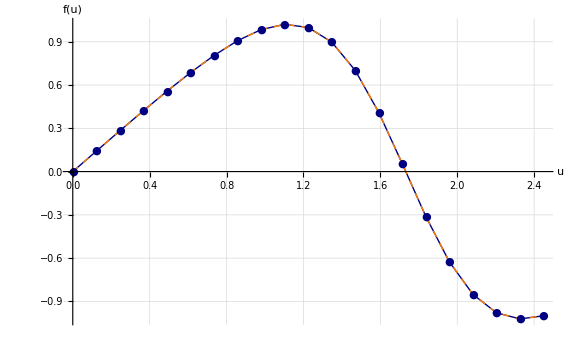

```mathematica
Export["./col_df_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",plot]
```

./col_df_N5_L6_m24_kappa1_sigma1.pdf